```mathematica
(*2. Считать данные из полученного входного файла в системе Wolfram Mathematica (учесть, что размерность графа может быть любой и параметры bi могут идти в произвольном порядке).*)
```

```mathematica
inFileName=StringJoin[NotebookDirectory[],"input.txt"];
fileStream=OpenRead[inFileName];
Is=Read[fileStream,{Word,Number}][[2]];
Us=Read[fileStream,{Word,Number}][[2]];
U=ReadList[fileStream,Expression,Us];
(*weight=ReadList[fileStream,String,Is];
weight=Sort[Table[StringSplit[weight[[i]],{"b","_","/*","*/"}], {i,Is}]]*)
UDirect=Table[U[[i,1]]->U[[i,2]],{i,Us}]
Close[fileStream];
```

{1->2,3->1,1->4,5->2,1->6,3->6,3->7,4->3,5->3,5->6,6->2,7->1,7->4}

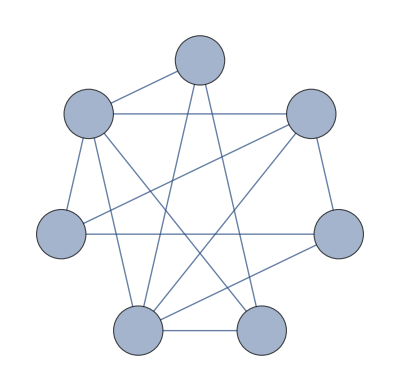

```mathematica
(*3. По полученным данным создать ориентированный граф с заданием стилей/*)
g = Graph[UDirect, GraphLayout->"CircularEmbedding", VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28], EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05], EdgeStyle->Thick]
```

```mathematica
(*4. Построить матрицу инцидентности для полученного графа.*)
(m=IncidenceMatrix[g])//MatrixForm
```

(-1 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | -1 | 0 | 0 | 0 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1)